```mathematica
q = 1.6*10^-19
V = 0.15*q
ϕ = 0
m = 0.1 * 9.1 * 10^-31
a = 50 * 10^-9
h = 6.6 * 10^-34
l = √(2 m V/h^2)
```

1.6×10^-19

2.4×10^-20

0

9.1×10^-32

1/20000000

6.6×10^-34

1.00138×10^8

```mathematica
NSolve[Tan[k a/2 ]==√((l^2- k^2)/k^2), k, Reals]
```

NSolve[Tan[k/20000000]==√((6.01653×10^16-k^2)/k^2),k,ℝ]

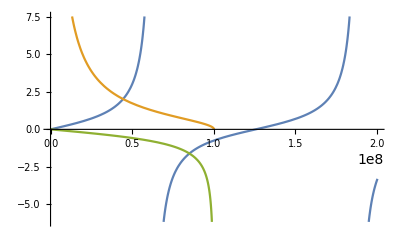

```mathematica
Plot[{Tan[k a/2 ],  √((l^2- k^2)/k^2), -√(k^2/(l^2-k^2)) }, {k,0, 2l}]
```